```mathematica
NotebookEvaluate[NotebookDirectory[]<>"/split_step.nb"];
```

GPE solver v1.4, RZ 2019

```mathematica
HarmonicTrap2D[0.5,1.0];
sizes={64,64};
timeStep=0.001;
k=+3;
contactInteractionFactor=4 Pi k;
initialize[];
gridReport
```

sizes | dim | len | max | min | delta | deltak | maxk
{64,64} | 2 | 4096 | {7.07107,5.} | {-7.07107,-5.} | {0.224478,0.15873} | {0.437346,0.618501} | {13.9951,19.792}

time | energies | moments | misc
(0) | (total | 2.87132
kinetic | 0.375
potential | 0.375
contact | 2.12132
virial | 4.24264) | (meanX | 0
meanY | 0
sigmaX | 1.
sigmaY | 0.707107
norm | 1.) | (steps | 0
A0 | 0.474383)

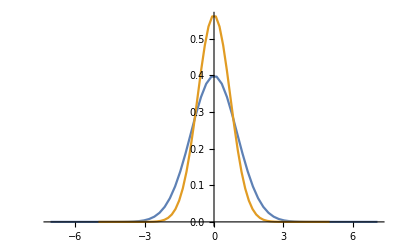

```mathematica
calcAllTable
p1=plotProjections
```

```mathematica
AbsoluteTiming[evolve["ite",30,10]]
```

{25.7091,Null}

time | energies | moments | misc
(30.) | (total | 1.84789
kinetic | 0.178216
potential | 0.924027
contact | 0.745643
virial | -0.00033685) | (meanX | 0
meanY | 0
sigmaX | 1.82697
sigmaY | 1.00678
norm | 1.) | (steps | 30000
A0 | 0.254874)

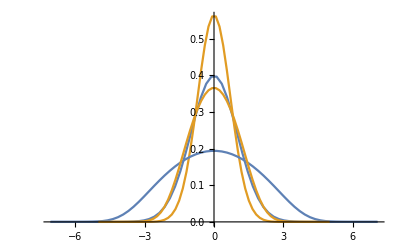

```mathematica
calcAllTable
p2=plotProjections;
Show[p1,p2,PlotRange->All]
```

```mathematica
reportEnergies
```

time | total | kinetic | potential | contact | virial
0 | 2.87132 | 0.375 | 0.375 | 2.12132 | 4.24264
3. | 1.84796 | 0.17862 | 0.920348 | 0.748991 | 0.0145269
6. | 1.84789 | 0.178222 | 0.923967 | 0.745698 | -0.0000930876
9. | 1.84789 | 0.178216 | 0.924026 | 0.745644 | -0.000332545
12. | 1.84789 | 0.178216 | 0.924027 | 0.745643 | -0.000336773
15. | 1.84789 | 0.178216 | 0.924027 | 0.745643 | -0.000336848
18. | 1.84789 | 0.178216 | 0.924027 | 0.745643 | -0.00033685
21. | 1.84789 | 0.178216 | 0.924027 | 0.745643 | -0.00033685
24. | 1.84789 | 0.178216 | 0.924027 | 0.745643 | -0.00033685
27. | 1.84789 | 0.178216 | 0.924027 | 0.745643 | -0.00033685
30. | 1.84789 | 0.178216 | 0.924027 | 0.745643 | -0.00033685

```mathematica
reportMoments
```

time | meanX | meanY | sigmaX | sigmaY | norm
0 | 0 | 0 | 1. | 0.707107 | 1.
3. | 0 | 0 | 1.81401 | 1.00898 | 1.
6. | 0 | 0 | 1.82674 | 1.00682 | 1.
9. | 0 | 0 | 1.82697 | 1.00678 | 1.
12. | 0 | 0 | 1.82697 | 1.00678 | 1.
15. | 0 | 0 | 1.82697 | 1.00678 | 1.
18. | 0 | 0 | 1.82697 | 1.00678 | 1.
21. | 0 | 0 | 1.82697 | 1.00678 | 1.
24. | 0 | 0 | 1.82697 | 1.00678 | 1.
27. | 0 | 0 | 1.82697 | 1.00678 | 1.
30. | 0 | 0 | 1.82697 | 1.00678 | 1.